```mathematica
By Le Chen.
Crated on Sat 30 Apr 2022 07:55:39 AM CDT
```

```mathematica
Integrate[r^(d-1)/(r^2(1+r^2)^(s/2)),{r,0,∞},Assumptions->{s>d-2,d>=3}]
```

(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2])

```mathematica
Solve[z == r^2/(1+r^2),r]
```

{{r→-(√z)/(√(1-z))},{r→(√z)/(√(1-z))}}

```mathematica
FullSimplify[(r^(d-1)/(r^2(1+r^2)^(s/2))/.r->√(z/(1-z)))D[√(z/(1-z)),z]//Expand,Assumptions->{0<z<1,s>d-2,d>=3}]
```

1/2 (1-z)^(1/2 (-d+s)) z^(-2+d/2)

```mathematica
Integrate[1/2 (1-z)^(1/2 (-d+s)) z^(-2+d/2),{z,0,1}]
```

ConditionalExpression[(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2]), Re[d-s]<2&&Re[d]>2]

```mathematica
(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2]) (2 π^(d/2))/Gamma[d/2]
```

(π^(d/2) Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(Gamma[d/2] Gamma[s/2])

```mathematica
FullSimplify[(π^(d/2) Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(Gamma[d/2] Gamma[s/2]),Assumptions->{s>d-2,d>=3}]
```

(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) Gamma[s/2])

```mathematica
(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])//TeXForm
```

\frac{2 \pi ^{d/2} \Gamma \left(\frac{1}{2} (-d+s+2)\right)}{(d-2) d \Gamma
   \left(\frac{s}{2}\right)}

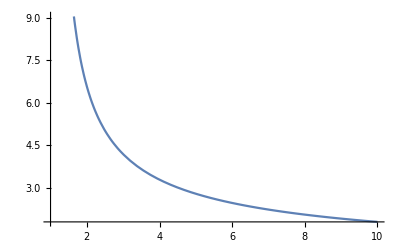

```mathematica
Plot[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])/.d->3,{s,1,10}]
```

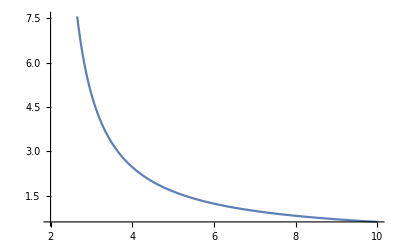

```mathematica
Plot[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])/.d->4,{s,2,10}]
```

```mathematica
Limit[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s->∞]
```

$Aborted

```mathematica
Limit[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s->∞,Assumptions->{d>=3}]
```

0

```mathematica
D[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s]//FullSimplify
```

(π^(d/2) Gamma[1/2 (2-d+s)] (-PolyGamma[0,s/2]+PolyGamma[0,1/2 (2-d+s)]))/((-2+d) d Gamma[s/2])